```mathematica
Remove["Global`*"]
z1 = 4.0/3.0;
z2 = 2.0/3.0;
p =  2.0/3.0;
q =  1.0/3.0;
η =  3.0/4.0;
X0 =  1.0;
```

```mathematica
SetOptions[{Plot,LogLogPlot,ListLogPlot, ListPlot, ListLogLogPlot, ListLogLinearPlot},
Frame-> True,
LabelStyle->{FontFamily->"Arial", FontSize->12},
AspectRatio->1];
SetOptions[{ListLogPlot, ListLogLinearPlot},  Joined->True, FrameLabel->{"x", " "}];
```

```mathematica
F6[z1_,z2_, p_, q_, η_, X0_]:=Module[{ζ,L,J, A,x, p1,p2,p3, expr, D2φ, Ampl,AA, title, φ},
ζ=1-η;
f[x_, λ_] := 2 ArcTanh[1- 2 x] + Log[p/q] + ((z1^ζ-z2^ζ)/(ζ X0^ζ+λ(x(z1^ζ-1)+(1-x)(z2^ζ-1))));
φ[x_, λ_] := x Log[p] + (1-x) Log[q] - x Log[x] -(1-x)Log[1-x]+ 1/λ Log[λ/ζ(x(z1^ζ-1)+(1-x)(z2^ζ-1)) + X0^ζ];

D2φ[x_, λ_] := -(1/x + 1/(1-x))-(λ(z1^ζ-z2^ζ)^2)/((ζ X0^ζ + λ(x(z1^ζ-1)+(1-x)(z2^ζ-1)))^2);
Ampl[x_, λ_] := 1/(√(-D2φ[x, λ] x(1-x)));
title ="p = "<>ToString[p]<> " z1 = "<>ToString[z1] <> " z2 =" <> ToString[z2] <> " η = " <> ToString[η];
L = Table[2^i,{i, Range[-10, 20, 1/2]}];
A= Table[{ λ, x /. FindRoot[f[x, λ], {x,9/10}]}, {λ, L}];
J = Table[{L[[i]],φ[A[[i,2]], L[[i]]]}, {i,1,Length[L]}];
J1 = Table[{L[[i]],Log[p z1 + q z2]}, {i,1,Length[L]}];
AA = Table[{L[[i]],Ampl[A[[i,2]], L[[i]]]}, {i,1,Length[L]}];
p1 = ListLogLinearPlot[A, FrameLabel->{"λ", "(x_λ^*)"}, PlotLabel->title, Joined->True];
p2 = ListLogLogPlot[{J, J1}, FrameLabel->{"λ", "Exponent, φ(x_λ)"}, PlotLabel->title, Joined->True];
p3 = ListLogLinearPlot[AA, FrameLabel->{"λ", "Amplitude"}, PlotLabel->title, Joined->True];
{p1, p2, p3}
]
```

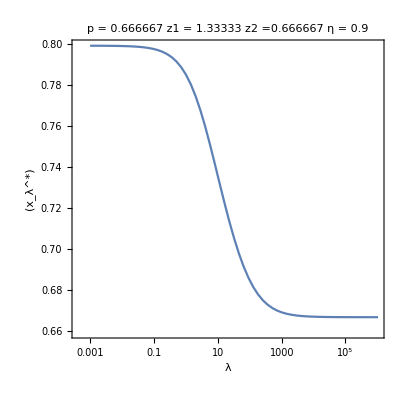
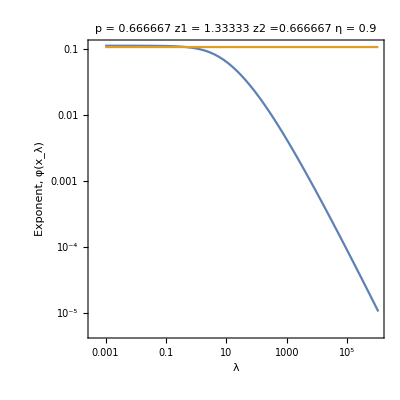
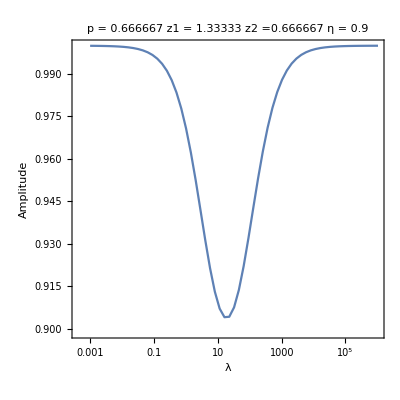

```mathematica
{p1,p2,p3} = F6[4.0/3.0,2.0/3.0, 2.0/3.0, 1.0/3.0, 9.0/10.0, 1.0]
```

```mathematica
Show[p1]
```

-Graphics-

```mathematica
Show[p2]
```

-Graphics-

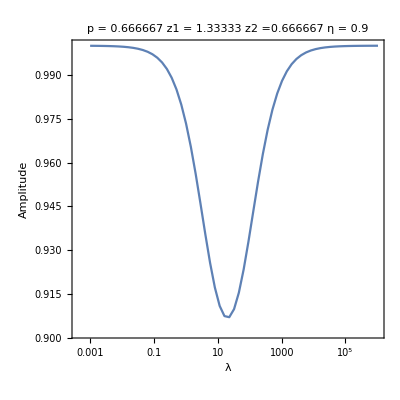

```mathematica
Show[p3]
```

```mathematica
Partition[dt,2,1]
```

{{{1,2},{3,9}},{{3,9},{7,4}},{{7,4},{9,9}}}

{0,0.5}

{{{9.8,0},{10.2,0}},{{9.8,0.5},{10.2,0.5}}}

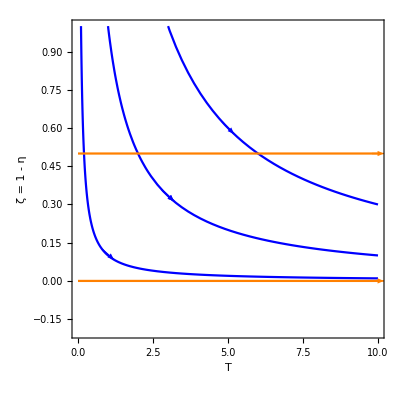

```mathematica
p1A = Plot[{1/(10 T), 1/T, 3/T}, {T, 0, 10}, PlotRange->{-0.2,1}, PlotStyle->{Blue}, FrameLabel->{"T", "ζ = 1 - η"}];
V = {0, 0.5}
p1B = Plot[V, {T, 0, 10}, PlotRange->{-0.2,1}, PlotStyle->{Orange} ];
Δ = 0.2;
L = {1/10, 1, 3};
T = {1,3, 5}; 
dtA = Table[{{T[[i]]-Δ, L[[i]]/(T[[i]]-Δ)}, {T[[i]]+Δ , L[[i]]/(T[[i]] + Δ)}},{i,1, 3} ];
dtB = Table[{{10-Δ, V[[i]]},{10+Δ, V[[i]]}}, {i,1,2}]
p2 = ListPlot[dtA];
p3 = Graphics[{Arrowheads[{{.05,0.5}}],Arrow/@Partition[dtA,2,1]},Frame->Automatic];
p3 = Graphics@{Blue,Arrowheads[{{.05,0.75}}],Arrow/@Partition[dt,2,1]};
p3B = Graphics@{Orange,Arrowheads[{{.05,0.75}}],Arrow/@Partition[dtB,2,1]};
Show[p1A,p1B, p3, p3B]
```

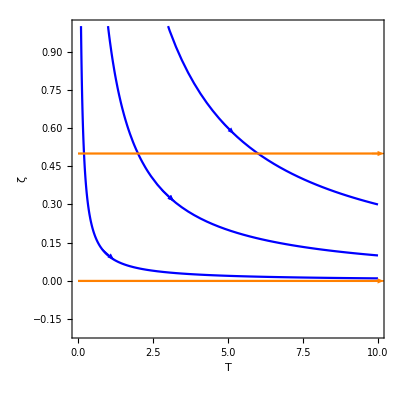
-Graphics-x10^-3

```mathematica
Overlay[{Show[p1A,p1B, p3, p3B,ImagePadding->{{Automatic,Automatic},{Automatic,15}}],Style[Row[{"x",10^"-3"}],Black,FontSize->12]},Alignment->{-0.91,1}]
```

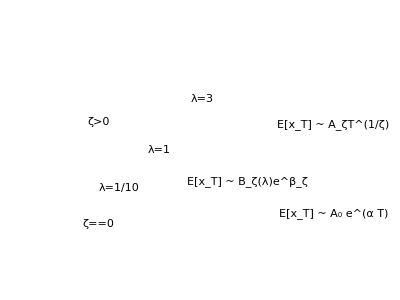

```mathematica
g1 = Graphics[{
Inset[Show[p1A, p1B, p3, p3B],ImageScaled[{0,0}],ImageScaled[{0,0}], {2,2}]
,
Text[Style[ToExpression["\\zeta=0",TeXForm,HoldForm],Medium],Scaled[{0.24,0.21}]]
,
Text[Style[ToExpression["\\zeta>0",TeXForm,HoldForm],Medium],Scaled[{0.24,0.61}]]
,
Text[Style["E[x_T] ~ A_0 e^(α T)",Medium],Scaled[{1.06,0.25}]]
,
Text[Style["E[x_T] ~ A_ζT^(1/ζ)",Medium],Scaled[{1.06,0.6}]]
,
Text[Style["E[x_T] ~ B_ζ(λ)e^β_ζ",Medium],Scaled[{0.76,0.375}]]
,
Text[Style["λ=1/10",Medium],Scaled[{0.31,0.35}]]
,
Text[Style["λ=1",Medium],Scaled[{0.45,0.5}]]
,
Text[Style["λ=3",Medium],Scaled[{0.60,0.7}]]
}]
```